# Fig. 2: Postselection Probability

## 1. Initialization and Operators

```mathematica
ClearAll[  "Global`*"];
```

```mathematica
{  dim, wp} = { 60, 35};
```

```mathematica
$MaxExtraPrecision = 2000;
```

```mathematica
a = N[ SparseArray[ Band[ { 1, 2}] -> Sqrt[ Range[ dim - 1]], { dim, dim}], wp];
```

```mathematica
adag = ConjugateTranspose[ a];
```

## 2. Coherent, Cat, and Photon-Added States

```mathematica
coherentState[ alpha_?NumericQ] := coherentState[ alpha] = Module[ { z = N[ alpha, wp]}, Normalize[ Table[ Exp[ -Abs[ z]^2/2] z^n/Sqrt[ n!], { n, 0, dim - 1}]] ];
```

```mathematica
catState[ r_?NumericQ, phi_?NumericQ, varphi_?NumericQ] := catState[ r, phi, varphi] = Module[ { alpha = N[ r Exp[ I phi], wp]}, Normalize[ coherentState[ alpha] + Exp[ I N[ varphi, wp]] coherentState[ -alpha]] ];
```

```mathematica
mpacs[ m_Integer?NonNegative, r_?NumericQ, phi_?NumericQ, varphi_?NumericQ] := mpacs[ m, r, phi, varphi] = Normalize[ Nest[ adag . # &, catState[ r, phi, varphi], m]];
```

## 3. Displacement Operator and Postselection Probability

```mathematica
displacementMatrix[ beta_?NumericQ] := displacementMatrix[ beta] = Module[ { b = N[ beta, wp]}, MatrixExp[ b adag - Conjugate[ b] a]];
```

```mathematica
psucc[ m_Integer?NonNegative, r_?NumericQ, phi_?NumericQ, varphi_?NumericQ, s_?NumericQ, delta1_?NumericQ, delta2_?NumericQ] := Module[ { psi, dp, dm, cH, cV, post}, psi = mpacs[ m, r, phi, varphi]; dp = displacementMatrix[ s/2] . psi; dm = displacementMatrix[ -s/2] . psi; cH = Cos[ N[ delta2, wp]/2]; cV = Exp[ I N[ delta1, wp]] Sin[ N[ delta2, wp]/2]; post = ((cH + cV) dp + (cH - cV) dm)/2; N[ Chop[ Re[ Conjugate[ post] . post], 10^-25], 16] ];
```

## 4. Fixed Parameters and Scan Values

```mathematica
{ r0, phi0, varphi0, s0, delta10, delta20, m0} = { 1, Pi/2, Pi/2, 1/2, Pi/2, 8 Pi/9, 1};
```

```mathematica
ss = { 0, 3/10, 1/2, 7/10, 1};
```

```mathematica
rs = { 1/2, 1, 2, 3, 4};
```

```mathematica
d2s = { 1, 3, 5, 7, 8} Pi/9;
```

```mathematica
ms = Range[ 0, 4];
```

## 5. Panel Data

### (a) Vary delta2 for Different s

```mathematica
dataA = Table[  { delta2, psucc[ m0, r0, phi0, varphi0, s, delta10, delta2]}, { s, ss}, { delta2, Pi/40, 17 Pi/18, Pi/40} ];
```

### (b) Vary phi for Different r

```mathematica
dataB = Table[  { phi, psucc[ m0, r, phi, varphi0, s0, delta10, delta20]}, { r, rs}, { phi, 0, 2 Pi, Pi/20} ];
```

### (c) Vary m for Different delta2

```mathematica
dataC = Table[  { m, psucc[ m, r0, phi0, varphi0, s0, delta10, delta2]}, { delta2, d2s}, { m, ms} ];
```

## 6. Line Styles and Markers

```mathematica
font = "Times New Roman";
```

```mathematica
pw = 230;
```

```mathematica
ph = 1.5 (0.64 pw + 45) - 45;
```

```mathematica
colors = { RGBColor[ 1, .24, .24], RGBColor[ .16, .24, 1], RGBColor[ 0, .68, .18], RGBColor[ 1, .5, 0], RGBColor[ .7, 0, .74]};
```

```mathematica
styles = MapThread[ Directive[ #1, AbsoluteThickness[ 2.7], AbsoluteDashing[ #2]] &, { colors, { { 4, 2}, { 1, 1.8}, { 4, 2}, { 4, 1.8, 1, 1.8}, { 5, 2}}}];
```

```mathematica
mark[ i_] := Graphics[ {  EdgeForm[ Directive[ colors[ [ i]], AbsoluteThickness[ 1.2]]], FaceForm[ White], Switch[ i, 1, Disk[ ], 2, Polygon[ { { 0, 1}, { -.866, -.5}, { .866, -.5}}], 3, Polygon[ { { 0, 1}, { 1, 0}, { 0, -1}, { -1, 0}}], 4, Rectangle[ { -1, -1}, { 1, 1}], 5, Polygon[ { { 0, -1}, { -.866, .5}, { .866, .5}}]]}, PlotRange -> { { -1.2, 1.2}, { -1.2, 1.2}}, ImagePadding -> 0, ImageSize -> 4, AspectRatio -> 1 ];
```

## 7. Axis Ticks

```mathematica
piLabel[ n_, d_] := If[ n == 0, "0", Row[ { If[ n == 1, "", n], "π/", d}]];
```

```mathematica
blank[ t_] := { #[ [ 1]], "", #[ [ 3]]} & /@ t;
```

```mathematica
ticks[ major_, minor_] := Join[  { #[ [ 1]], #[ [ 2]], { .017, 0}} & /@ major, { #, "", { .009, 0}} & /@ Select[ minor, Min[ Abs[ # - major[ [ All, 1]]]] > 10^-7 &] ];
```

```mathematica
xt = {  ticks[ Table[ { n Pi/9, piLabel[ n, 9]}, { n, 0, 8, 2}], Range[ 0, 17] Pi/18], ticks[ { { 0, "0"}, { Pi/2, "π/2"}, { Pi, "π"}, { 3 Pi/2, "3π/2"}, { 2 Pi, "2π"}}, Range[ 0, 40] Pi/20], ticks[ Table[ { n, n}, { n, 0, 4}], Range[ 0, 20]/5] };
```

```mathematica
yt = Table[ { n/20, If[ Mod[ n, 4] == 0 && n <= 20, { "0.0", "0.2", "0.4", "0.6", "0.8", "1.0"}[ [ n/4 + 1]], ""], { If[ Mod[ n, 4] == 0, .017, .009], 0}}, { n, 0, 23}];
```

## 8. Legends

```mathematica
labels = {  Row[ { Style[ "s", Italic], " = ", #}] & /@ { "0.0", "0.3", "0.5", "0.7", "1.0"}, Row[ { Style[ "r", Italic], " = ", #}] & /@ { "0.5", "1", "2", "3", "4"}, Row[ { Subscript[ Style[ "δ", Italic], 2], " = ", piLabel[ #, 9]}] & /@ { 1, 3, 5, 7, 8} };
```

```mathematica
legend[i_] := With[{columns = If[i == 2, 3, 2]}, Grid[Flatten /@ Partition[Table[{Graphics[{styles[[k]], Line[{{0, 0.5}, {1, 0.5}}], Inset[mark[k], {0.5, 0.5}, Center, Offset[{6., 6.}]]}, PlotRange -> {{0, 1}, {0, 1}}, ImagePadding -> 0, ImageSize -> {18, 10.5}], labels[[i,k]]}, {k, 5}], columns, columns, 1, {}], Alignment -> Left, Spacings -> {0.25, 0.06}, BaseStyle -> {FontFamily -> font, FontSize -> 34, Black}]];
```

## 9. Panel Formatting

```mathematica
plot[data_, i_] := With[{left = If[i == 1, 65, 6], right = If[i == 3, 10, 6]}, ListLinePlot[data, PlotStyle -> styles, Axes -> False, Frame -> True, FrameLabel -> {{Subscript["δ", 2], "φ", Style["m", Italic]}[[i]], If[i == 1, Subscript[Style["P", Italic], "s"], None]}, FrameTicks -> {{If[i == 1, yt, blank[yt]], blank[yt]}, {xt[[i]], blank[xt[[i]]]}}, FrameStyle -> Directive[Black, AbsoluteThickness[1.6]], FrameTicksStyle -> Directive[Black, AbsoluteThickness[1.2], FontSize -> 34, FontFamily -> font], LabelStyle -> {FontFamily -> font, FontSize -> 38, Black, ScriptSizeMultipliers -> 0.85}, BaseStyle -> {FontFamily -> font, FontSize -> 18}, PlotRange -> {{{0, 17*(Pi/18)}, {0, 2*Pi}, {-0.05, 4.05}}[[i]], {0, 1.2}}, Sequence[PlotRangePadding -> None, GridLines -> {None, {1}}, GridLinesStyle -> Directive[GrayLevel[0.8], AbsoluteThickness[1.1], AbsoluteDashing[{5, 4}]]], PlotRangeClipping -> False, ImagePadding -> 1.5*{{left, right}, {60, 3}}, ImageSize -> 1.5*{pw + left + right, ph + 60} + {12, 0}, AspectRatio -> (1.5*(ph + 60) - 1.5*63)/(1.5*(pw + left + right) - 1.5*(left + right) + 12), Background -> White, Epilog -> Join[Flatten[Table[(Inset[mark[k], #1, Center, Offset[{6., 6.}]] & ) /@ data[[k,DeleteDuplicates[Append[Range[1, Length[data[[k]]], If[i == 3, 1, 3]], Length[data[[k]]]]]]], {k, 5}], 1], {Inset[Style[StringJoin["(", FromCharacterCode[96 + i], ")"], FontFamily -> font, FontSize -> 44, FontWeight -> Bold, Black], Offset[{28, 4}, Scaled[{0, 0}]], {Left, Bottom}], Inset[legend[i], Scaled[{0.98, 0.98}], {Right, Top}]}]]];
```

## 10. Assemble and Display Fig. 2

```mathematica
figAll = Module[ {  panels = MapIndexed[ plot[ #1, First[ #2]] &, { dataA, dataB, dataC}], widths = 1.5 (pw + { 71, 12, 16}) + 12, h = 1.5 (ph + 80), gap = 12, total}, total = Total[ widths] + 2 gap; Magnify[ Graphics[ Table[  Inset[ panels[ [ i]], { Total[ Take[ widths, i - 1]] + gap (i - 1), h}, { Left, Top}, { widths[ [ i]], h}], { i, 3}], PlotRange -> { { 0, total}, { 0, h}}, ImagePadding -> 0, PlotRangePadding -> None, ImageSize -> { total, h}, AspectRatio -> h/total, Background -> White], 1.5] ];
```

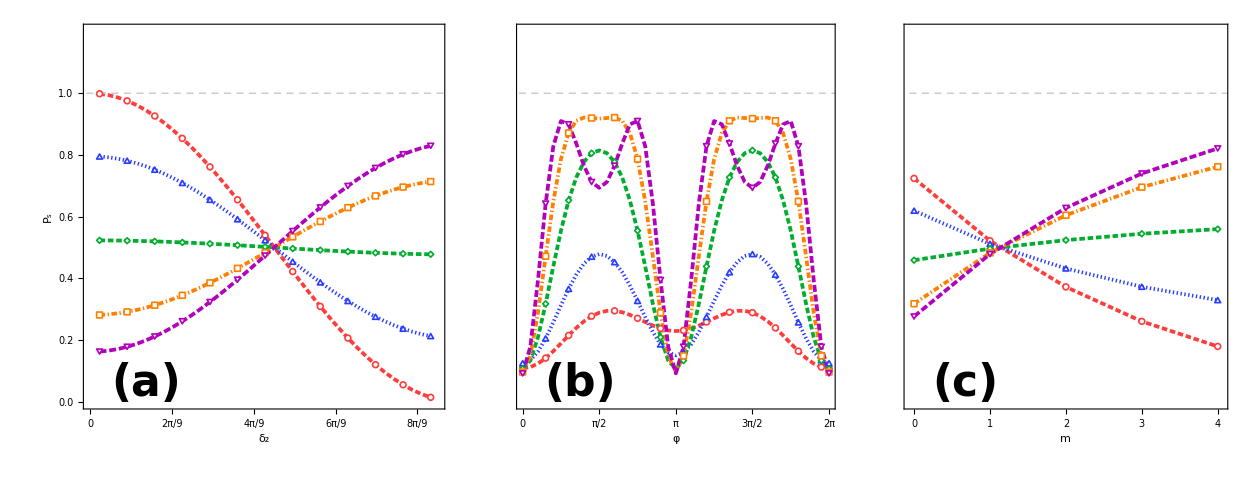

```mathematica
figAll
```

## 11. Export PNG (Optional)

```mathematica
Export[FileNameJoin[{NotebookDirectory[], "Fig.2.png"}], Rasterize[figAll, "Image", RasterSize -> {4145, Automatic}, Background -> White], "PNG"];
```